# Applying Kepler’s Laws: Finding the Orbit of Mars

## by Daniel Hwang, Daniel Arad, and Nikhil Thakur (with help from Osher Lerner!) MVC Spring 2019

## Defining Variables

We begin by initializing the various variables that describe the properties of Mars’s orbit.

Semi-major axis (in kilometers): a

```mathematica
a=227.92*10^6
```

Semi-minor axis (in kilometers): b

```mathematica
b=2.2692381163 * 10^8
```

Orbital period (in seconds): T

```mathematica
T=5.9355072*10^7
```

The infinitesimal area swept out by the radius vector – the vector with tail at the sun and tip at Mars’s position – in an infinitesimal time 𝕕t (in kilometers^2): ⅆA/ⅆt = c

We know that this is constant from Kepler’s Second Law.

```mathematica
c=(π*a*b)/T
```

Orbit eccentricity: e

```mathematica
e=0.0933941
```

Orbit directrix: d

```mathematica
d=√((b^2(1-e^2))/e^2)
```

Magnitude of the radius vector as a function of theta as a function of time (in kilometers): r

```mathematica
r[θ_[t]]=(e*d)/(1+e*Cos(θ[t]))
```

## Deriving the Shape of Mars’s Orbit

We then use the previously defined variables in order to derive the shape of Mars’s orbit.

### Deriving Theta as a Function of Time: s

To derive theta as a function of time, we notice that the infinitesimal area swept out by the radius vector in an infinitesimal time 𝕕t is an infinitesimally small triangle. This triangle’s base is the segment connecting the sun and Mars, meaning that the base has length r[θ[t]], while its height is the instantaneous change in arclength, meaning that the height has length r · ⅆθ/ⅆt. Therefore, the area of this triangle ⅆA/ⅆt can be calculated as

```mathematica
ⅆA/ⅆt=1/2*r[θ[t]]*r[θ[t]]*θ'[t]=1/2*(r[θ_[t]])^2*θ'[t]
```

Therefore, from our definition of c, we have

```mathematica
ⅆA/ⅆt=1/2*(r[θ_[t]])^2*θ'[t]=c
```

Since c is a constant, this is an expression that gives θ in terms of time. Additionally, this expression must always hold, meaning that we can create an ordinary differential equation that evaluates θ[t] = s at every timestep.

```mathematica
s=NDSolve[{1/2*((e*d)/(1+e*Cos[θ[t]]))^2*θ'[t]==c,θ[0]==0},θ,{t,0,T}]
```

{{θ→InterpolatingFunction[…]}}

### Graphing the Orbit Ellipse

Now that we have theta as a function of time, we can graph the path Mars would trace after T time (its period). This means that the graph should be Mars’s orbit ellipse, and sure enough, it is!

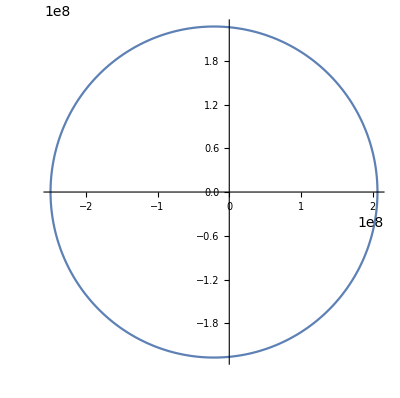

```mathematica
curve=ParametricPlot[Evaluate[CoordinateTransform["Polar"->"Cartesian",{(e*d)/(1+e*Cos[θ[t]]),θ[t]}]/.s],{t,0,T}]
```

## Animating Mars’s Orbit Over Time

We’re almost done! All we need to do now is plot Mars’s motion over time.

### Re-parameterizing Mars’s Position: From Polar to Cartesian

In order to graph Mars’s position at each time point, we need to re-parameterize our position equation in terms of Cartesian coordinates.

X

```mathematica
u[t_]:=First[Evaluate[First[CoordinateTransform["Polar"->"Cartesian",{(e*d)/(1+e*Cos[θ[t]]),θ[t]}]]/.s]]
```

Y

```mathematica
First[Evaluate[Last[CoordinateTransform["Polar"->"Cartesian",{(e*d)/(1+e*Cos[θ[t]]),θ[t]}]]/.s]]
```

### Animating Mars’s Position

Now we can animate Mars’s position!

```mathematica
Animate[Show[curve,Graphics[{PointSize[Large],Red,Point[{u[R],v[R]}]}]],{R,0,T}]
```

## Just for fun:

Perihelion

```mathematica
(e*d*Cos[θ[0]])/(1+e*Cos[θ[0]]) /.s
```

{2.06634×10^8}